# Evolved Gradient Discrimination

1. Show that absolute sensor agent internally calculates derivative and behaves otherwise the same
3. ds/dm for different amplitudes of gradient (invariant ?)
4. Reinforment learning of catch/avoid

## Import

### Setup and libraries

```mathematica
ClearAll["Global`*"]
Clear["Global`*"]
Needs["PlotLegends`"]
<<"~thomasbuhrmann/Code/Mathematica/Dynamica/Dynamica.m";

SetOptions[Plot,BaseStyle->{FontFamily->"Times",FontSize->14}];
```

Dynamica (Version 1.0.5 - 12/6/11), Copyright(c) 1993-2011 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

General::obspkg: "VectorFieldPlots`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

### For graphics export

```mathematica
With[{temp=Directory[]},If[$Failed=!=SetDirectory["~/Library/Application\ Support/Adobe/Fonts/"],If[!MemberQ[FileNames[],"Mathematica"],CreateDirectory["Mathematica"];
Run["/bin/ln -s "<>$InstallationDirectory<>"/SystemFiles/Fonts/Type1 "<>$HomeDirectory<>"/Library/Application\\ Support/Adobe/Fonts/Mathematica/"];
SetDirectory["Mathematica"];
Print[Style["Created symbolic link\n",Green],FileNames[],Style["\nin folder\n",Green],Directory[]],Print[Style["Nothing to be done, folder already exists.\nTo re-install, first remove\n",Red],Directory[]<>"/Mathematica"]];
SetDirectory[temp]]]

figExpPath="~thomasbuhrmann/Documents/Publications/SMCs/figures/";
```

Nothing to be done, folder already exists.
To re-install, first remove
/Users/thomasbuhrmann/Library/Application Support/Adobe/Fonts/Mathematica

/Users/thomasbuhrmann

### Import data

```mathematica
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/DerivativeOnly/HighFrameRateInc/12_07_05__18_03_56"; 
dt=1/200;
(*dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/DerivativeOnly/12_06_25__14_58_12"; dt=0.02;*)
SetDirectory[dirName];
(*genFit=Import["Generalization.txt", "Table"];*)
genFit=Import["GeneralizationNoBoundary.txt", "Table"];
data = Import["State.txt", "Table"];
stateNames=data[[1]]
state = data[[2;;-2]];
numStates=Dimensions[stateNames];
numData=Length[state]

fitXml = Import["GA_Progress.xml"];
bestFitness=Cases[fitXml,XMLElement["Generation",{_,"BestFitness"->fit_,_},___]->fit,Infinity];
avgFitness=Cases[fitXml,XMLElement["Generation",{_,_,"AverageFitness"->fit_},___]->fit,Infinity];
bestFitness=ToExpression[bestFitness];
avgFitness=ToExpression[avgFitness];
```

{Angle,AngularVel,NeuralExtInput0,NeuralExtInput1,NeuralExtInput2,NeuralOutput0,NeuralOutput1,NeuralOutput2,NeuralState0,NeuralState1,NeuralState2,PosX,PosY,Sensor,SensorDer,VelX,VelY}

40000

## Functions

```mathematica
TtoI[time_]:=Floor[time/dt];
NtoI[name_]:=Position[stateNames, name][[1,1]];
NtoD[name_,t0_,tn_]:=Table[state[[i,NtoI[name]]],{i,t0,tn}];
time = Range[0,100.0,dt];
padds={{30,10},{20,20}};
plotOptions = {PlotJoined->True,ImagePadding->padds};

SetTrial[tr_,startAt_,duration_,T_]:={i0,in}={1+TtoI[tr*T+startAt],TtoI[tr*T+startAt+duration]};

TimeTrajectory[name_,t1_,t2_]:=Transpose[{time[[1;;(t2-t1+1)]],NtoD[name,t1,t2]}];
TimeTrajectoryData[data_,t1_,t2_]:=Transpose[{time[[1;;(t2-t1+1)]],data}];

TimeTrajectory2d[name1_, name2_,t0_,tn_]:=Transpose[{time[[1;;tn-t0+1]],NtoD[name1,t0,tn],NtoD[name2,t0,tn]}];

PhaseTrajectory[name1_, name2_,t0_,tn_,m1_:1,m2_:1]:=Transpose[{m1*NtoD[name1,t0,tn],m2*NtoD[name2,t0,tn]}];

PhaseTrajectory3d[name1_, name2_,name3_,t0_,tn_,m1_:1,m2_:1,m3_:1]:=Transpose[{m1*NtoD[name1,t0,tn],m2*NtoD[name2,t0,tn],m3*NtoD[name3,t0,tn]}];

TimePlot[name_,t0_,tn_,options_:{}] := ListLinePlot[TimeTrajectory[name,t0,tn], Join[plotOptions,options]];
DataPlot[data_,t0_,tn_,options_:{}] := ListLinePlot[TimeTrajectoryData[data,t0,tn], Join[plotOptions,options],AxesLabel->{"time"}];

TimePlot2d[name1_,name2_,t0_,tn_,options_:{}]:=Graphics3D[{Line[TimeTrajectory2d[name1,name2,t0,tn],VertexColors->1-Range[0,1,1/(tn-t0)]]},options,AxesLabel->{"time",name1,name2}];

PhasePlot[name1_,name2_,t0_,tn_,options_:{},m1_:1,m2_:1]:=Graphics[Line[PhaseTrajectory[name1,name2,t0,tn,m1,m2],VertexColors->0.8-Range[0,0.8,0.8/(tn-t0)]],Axes->True,AxesLabel->{name1,name2},options,AspectRatio->1.0];

PhasePlot3d[name1_,name2_,name3_,t0_,tn_,options_:{},m1_:1,m2_:1,m3_:1]:=Graphics3D[Line[PhaseTrajectory3d[name1,name2,name3,t0,tn,m1,m2,m3],VertexColors->1-Range[0,1,1/(tn-t0)]],Axes->True,AxesLabel->{name1,name2},options,AspectRatio->1.0];

Colorbar[colorFunction_: Automatic,min_:0,max_:1,divs_: 25]:=DensityPlot[y,{x,0,1},{y,min,max},AspectRatio->10,PlotRangePadding->0,PlotPoints->{2,divs},MaxRecursion->0,FrameTicks->{None,Automatic,None,None},ColorFunction->colorFunction];

G2D=Graphics[{},AlignmentPoint->Center,AspectRatio->1,Axes->False,AxesLabel->None,BaseStyle->{FontFamily->"Arial",FontSize->12},Frame->True,FrameStyle->Directive[Black],FrameTicksStyle->Directive[10,Black],ImagePadding->{{20,5},{15,5}},LabelStyle->Directive[Black],PlotRange->All,PlotRangeClipping->False,PlotRangePadding->Scaled[0.02]];

G2D2=Graphics[{},AlignmentPoint->Center,AspectRatio->1,Axes->False,AxesLabel->None,BaseStyle->{FontFamily->"Arial",FontSize->12},Frame->True,FrameStyle->Directive[Black],FrameTicksStyle->Directive[10,Black],ImagePadding->{{20,5},{15,5}},LabelStyle->Directive[Black],PlotRangeClipping->True,PlotRangePadding->Scaled[0.02]];

G3D=Graphics[{},AlignmentPoint->Center,BaseStyle->{FontFamily->"Arial",FontSize->10},ImagePadding->{{20,5},{15,10}},LabelStyle->Directive[Black]];

Rastered[g_,fnm_,size_,options_]:=Module[{g1,axes,plot},
g1=Show[g,options,ImageSize->size];
(*axes=Graphics[{},FilterRules[AbsoluteOptions[g1],Except[FrameTicks]]];*)
axes=Graphics[{},AbsoluteOptions[g1]];
plot=Show[g1,FrameStyle->Directive[Opacity[0]]];
plot=Magnify[plot,5];
plot=Rasterize[plot,"Image",Background->None];
(*plot=ImageResize[Rasterize[plot,"Image",ImageResolution->72*2,Background->None],Scaled[1/2]];*)
plot =Show[plot,ImageSize->ImageDimensions[axes]];
Export[fnm<> "Axes.eps",axes];
Export[fnm<>"Plot.png",plot];
Overlay[{plot,axes}]
];

Rastered3d[g_,fnm_,size_,options_]:=Module[{g1,axes,plot},
g1=Show[g,options,ImageSize->size];
axes=Graphics3D[{},FilterRules[AbsoluteOptions[g1],Except[FrameTicks]]];
plot=Show[g1,Boxed->False,BoxStyle->Directive[Opacity[0]],AxesStyle->Directive[Opacity[0]]];
plot=Magnify[plot,2];
plot=Rasterize[plot,"Image",Background->None,ImageResolution->72];
(*plot=ImageResize[Rasterize[plot,"Image",ImageResolution->72*2,Background->None],Scaled[1/2]];*)
plot =Show[plot,ImageSize->ImageDimensions[axes]];
Export[fnm<> "Axes.eps",axes];
Export[fnm<>"Plot.png",plot, Background->None];
Overlay[{axes,plot}]
];
```

## CTRNN Definition

### Differential equations

General definition of the two-node network, and specialization via replacement rules.

```mathematica
σ[x_]=1/(1+ⅇ^-x);

maxp = 60;

neuron= DynamicalSystem[
{(-y+w σ[y+θ]+J)/τ},
{{y,-maxp,maxp}},
{{w,-maxp,maxp},
{θ,-maxp,maxp},
{J,-50,50},
{τ,0.5,20}}];

couple =DynamicalSystem[
{(-y1+w11 σ[y1+θ1]+w21 σ[y2+θ2]+J)/τ1,(-y2+w12 σ[y1+θ1]+w22 σ[y2+θ2])/τ2},
{{y1,-maxp,maxp},{y2,-maxp,maxp}},
{{w11,-maxp,maxp},{w12,-maxp,maxp},{w21,-maxp,maxp},{w22,-maxp,maxp},{θ1,-maxp,maxp},{θ2,-maxp,maxp},{τ1,0.5,20},{τ2,0.5,20},{J,-50,50}}];
```

### Specialization

```mathematica
hidden = neuron/.{w->7.54563,θ->-4.0057,τ->1.0,J->0};
output = neuron/.{w->0.0,θ->1.57389,τ->1.0,J->0};
inW=9.79266;

network = couple/.{w11->7.54563,w21->0,w12->-2.07816, w22->0.0,θ1->-4.0057,θ2->1.57389,τ1->1.0,τ2->1.0,J->0};
With[{ε=10^-7},networko=TransformDynamicalSystem[network,{{o1,ε,1-ε},{o2,ε,1-ε}},{σ[y1+θ1],σ[y2+θ2]}]];
With[{ε=10^-7},hiddeno=TransformDynamicalSystem[hidden,{{o,ε,1-ε}},{σ[y+θ]}]];
With[{ε=10^-7},outputo=TransformDynamicalSystem[output,{{o,ε,1-ε}},{σ[y+θ]}]];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

## Task

Analyse the Gaussian function and how its gradient changes for different amplitudes and widths. The steepest slope is always at w.

### Slope of the gradient

{{x→-w},{x→w}}

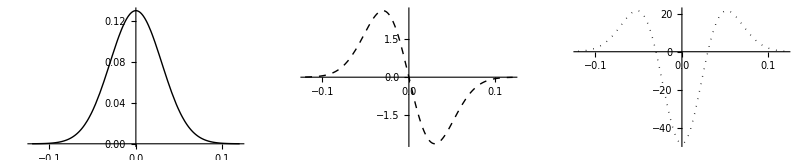

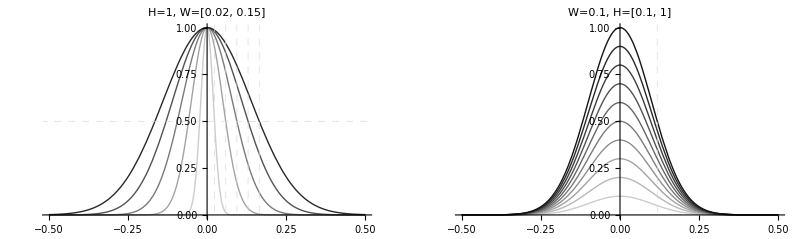

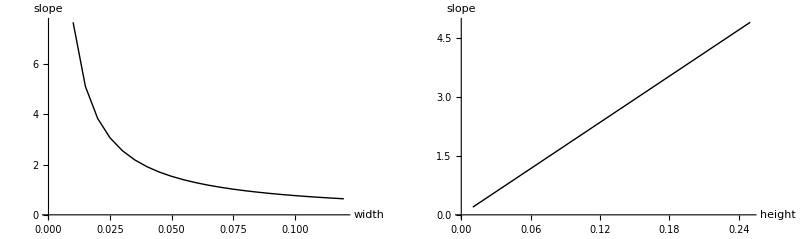

```mathematica
Gaus[x_,h_,w_]:=h Exp[-x^2/(2 w^2)];
GausDx[x_,h_,w_]:=-h/w^2 x Exp[-x^2/(2 w^2)];
Solve[D[-h/w^2 x Exp[-x^2/(2 w^2)],x]==0,x] (* Maxima of Gaussian derivative are exactly at w ! *)
GausDDx[x_,h_,w_]=-(ⅇ^(-x^2/(2 w^2)) h)/w^2+(ⅇ^(-x^2/(2 w^2)) h x^2)/w^4;

HWHM[w_]:=0.5*2.3548*w;

GausPos[y_,h_,w_]:=FindRoot[Gaus[x,h,w]==y,{x,w,0,5w}] [[1,2]];
GausDxPosInner[y_,h_,w_]:=FindRoot[GausDx[x,h,w]==y,{x,0,0,w}] [[1,2]];
GausDxPosOuter[y_,h_,w_]:=FindRoot[GausDx[x,h,w]==y,{x,2w,w,5w}] [[1,2]];

widthRange=Range[0.02,0.15,0.03];
heightRange=Range[0.1,1,0.1];
hwhm=HWHM[widthRange];

GrayLevelTable[steps_]:=Table[GrayLevel[i],{i,0.8,0.0,-0.8/steps}];
widthColors=GrayLevelTable[Length[widthRange]];
heightColors=GrayLevelTable[Length[heightRange]];

gaussWidthPlot=Plot[Evaluate[Table[Gaus[v,1,width],{width,widthRange}]],{v,-0.5,0.5},PlotRange->All,PlotStyle->widthColors,GridLines->{hwhm,{0.5}},GridLinesStyle->Dashed,PlotLabel->"H=1, W=[0.02, 0.15]"];

gaussHeightPlot=Plot[Evaluate[Table[Gaus[v,height,0.1],{height,heightRange}]],{v,-0.5,0.5},PlotRange->All,PlotStyle->heightColors,GridLines->{{HWHM[0.1]},{}},GridLinesStyle->Dashed,PlotLabel->"W=0.1, H=[0.1, 1]"];

hh=0.13;ww=0.03;
gaussDxPlot=GraphicsRow[{
Plot[Gaus[x,hh,ww],{x,-4ww,4ww},PlotStyle->Black,PlotRange->All],Plot[GausDx[x,hh,ww],{x,-4ww,4ww},PlotStyle->{Black,Dashed},PlotRange->All],
Plot[GausDDx[x,hh,ww]/3,{x,-4ww,4ww},PlotStyle->{Black,Dotted},PlotRange->All]
},ImageSize->800]

(*Rasterize[%,ImageResolution->200]*)

GraphicsRow[{gaussWidthPlot,gaussHeightPlot},ImageSize->800]

(* Plot slope of gaussian at hwhm for different widths *)
widthRange=Range[0.01,0.12,0.005]; Dimensions[widthRange];
heightRange=Range[0.01,0.25,0.01];Dimensions[heightRange];
slopes=Table[GausDx[HWHM[width],0.13,width],{width,widthRange}];
widthSlopePlot=ListLinePlot[Transpose[{widthRange,Abs[slopes]}],AxesLabel->{width,slope},PlotStyle->Black,AxesOrigin->{0,0}];

(* Plot slope of gaussian at hwhm for different heights *)
slopes=Table[GausDx[HWHM[0.03],height,0.03],{height,heightRange}];
heightSlopePlot=ListLinePlot[Transpose[{heightRange,Abs[slopes]}],AxesLabel->{height,slope},PlotStyle->Black,AxesOrigin->{0,0}];

GraphicsRow[{widthSlopePlot,heightSlopePlot},ImageSize->800]
```

### SMC with absolute sensor

Shows for every position x (with Gaussian centred at origin), the difference in sensor reading as one moves a distance dx away from x. This tries to replicate the diagrams of Alex and Andreas, in which for a given motor command (a distance moved in a certain direction), the plot shows whether one will encounter a sensor reading s’ when the current reading is s.

#### Change in sensor value

First, change in s as a function of change in position (ds/dx), given initial position. Then, change in s as a function of change in position (ds/dx) given initial sensor reading s

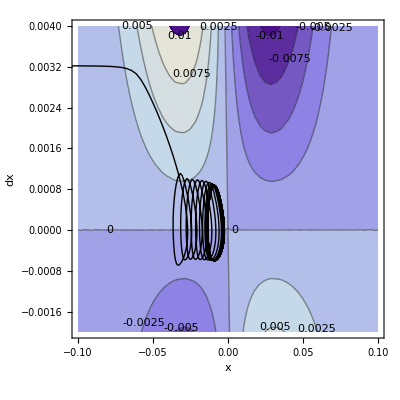

```mathematica
xmin=-0.1; xmax=0.1;
dxmin=-0.002; dxmax=0.004;
i0=1; in=900;
hh=0.13;
ww=0.03;

(* Underlying sensor surface for all possible moves  *)
smc3d=Plot3D[(Gaus[x+dx,hh,ww]-Gaus[x,hh,ww])/1,{x,xmin,xmax},{dx,dxmin,dxmax},AxesLabel->{"x","dx"},ColorFunction->(ColorData["DarkRainbow"][#3]&),MeshFunctions->{#3&},Mesh->10];

smcCtr=ContourPlot[(Gaus[x+dx,hh,ww]-Gaus[x,hh,ww])/1,{x,xmin,xmax},{dx,dxmin,dxmax},ContourLabels->True,FrameLabel->{"x","dx"}];

(* Overlay actual trajectories *)
posTr=NtoD["PosY",i0,in];
posDtTr=Differences[posTr];
posTr=posTr[[1;;-2]];
sTr=Gaus[posTr,hh,ww];
sDx=Gaus[posTr+posDtTr,hh,ww]-sTr + 0.0002;

SetTrial[10,0,9.9,10];
ww=0.08;
posTrAv=NtoD["PosY",i0,in];
posDtTrAv=Differences[posTrAv];
posTrAv=posTrAv[[1;;-2]];
sTrAv=Gaus[posTrAv,hh,ww];
sDxAv=Gaus[posTrAv+posDtTrAv,hh,ww]-sTrAv + 0.0002;
ww=0.03;

catchSMCtrajX3d=Transpose[{posTr,posDtTr,sDx}];
catchSMCtrajX2d=Transpose[{posTr,posDtTr}];
catchSMCtrajS3d=Transpose[{posDtTr,sTr,sDx}];
catchSMCtrajXPl3d=Graphics3D[{Thick,Line[catchSMCtrajX3d,VertexColors->1-Range[0,1,1/(in-i0)]]},Axes->True,BoxRatios->1.0];
catchSMCtrajXPl2d=Graphics[{Thick,Line[catchSMCtrajX2d,VertexColors->1-Range[0,1,1/(in-i0)]]},Axes->True];
catchSMCtrajSPl3d=Graphics3D[{Thick,Line[catchSMCtrajS3d,VertexColors->1-Range[0,1,1/(in-i0)]]},Axes->True];

GraphicsRow[{Show[smc3d,catchSMCtrajXPl3d],Show[smcCtr,catchSMCtrajXPl2d]},ImageSize->800]
```

Surface symmmetry: f(x+dx) = f(-x-dx).  This is the Gaussian shifted linearly along dx, and in form of G itself along x. The latter happens because the dependent variable ds is measured relative to varying starting position on the Gaussian.

```mathematica
opacity=0.5;
specul=30;
colP=Yellow;
colN=Cyan;
boxRatio=1;

smcDs3dPos=Plot3D[(Gaus[GausPos[y,hh,ww]+dx,hh,ww]-y),{dx,dxmin,dxmax},{y,0.001,hh},AxesLabel->{"dx","s","ds"},MeshFunctions->{#3&},Mesh->10,PlotStyle->{colP,Opacity[0.5],Specularity[White,specul]},BoxRatios->boxRatio];

smcDs3dNeg=Plot3D[Gaus[-GausPos[y,hh,ww]+dx,hh,ww]-y,{dx,dxmin,dxmax},{y,0.001,hh},AxesLabel->{"dx","s","ds"},MeshFunctions->{#3&},Mesh->10,PlotStyle->{colN,Opacity[1.0],Specularity[White,specul]},BoxRatios->boxRatio];

smcDs3d=Plot3D[{Gaus[GausPos[y,hh,ww]+dx,hh,ww]-y,Gaus[-GausPos[y,hh,ww]+dx,hh,ww]-y},{dx,dxmin,dxmax},{y,0.001,hh},AxesLabel->{"dx","s","ds"},MeshFunctions->{#3&},Mesh->{{0}},PlotStyle->{{colP,Opacity[0.5],Specularity[White,specul]},{colN,Opacity[1],Specularity[White,specul]}},BoxRatios->boxRatio];

GraphicsGrid[{
{Show[smcDs3dPos,catchSMCtrajSPl3d],Show[smcDs3dNeg,catchSMCtrajSPl3d]},
{Show[smcDs3d,catchSMCtrajSPl3d],SpanFromLeft}
},ImageSize->800]
```

-Graphics-

#### Next sensor value map

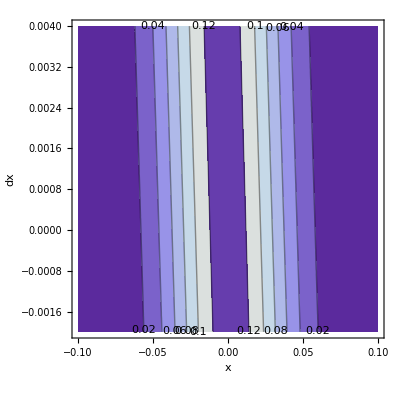

```mathematica
smc3d=Plot3D[Gaus[x+dx,hh,ww],{x,xmin,xmax},{dx,dxmin,dxmax},AxesLabel->{"x","dx"},ColorFunction->(ColorData["DarkRainbow"][#3]&),MeshFunctions->{#3&},Mesh->5];
smcCtr=ContourPlot[Gaus[x+dx,hh,ww],{x,xmin,xmax},{dx,dxmin,dxmax},ContourLabels->True,FrameLabel->{"x","dx"}];

ssdx=Gaus[posTr+posDtTr,hh,ww];
catchSMCtrajX3dSS=Transpose[{posTr,posDtTr,ssdx}];
catchSMCtrajX3dSSPl =Graphics3D[{Thick,Line[catchSMCtrajX3dSS,VertexColors->1-Range[0,1,1/(in-i0)]]},Axes->True,BoxRatios->1.0];

GraphicsRow[{Show[smc3d,catchSMCtrajX3dSSPl],smcCtr},ImageSize->800]
```

When plotted as function of position, this is basically just the gaussian at different positions dx.

```mathematica
catchSMCtrajS3dSS=Transpose[{posDtTr,sTr,ssdx}];
catchSMCtrajS3dSSPl =Graphics3D[{Thick,Line[catchSMCtrajS3dSS,VertexColors->1-Range[0,1,1/(in-i0)]]},Axes->True,BoxRatios->1.0];

smcSS3dPos=Plot3D[Gaus[GausPos[y,hh,ww]+dx,hh,ww],{dx,dxmin,dxmax},{y,0.001,hh},AxesLabel->{"dx","s"},MeshFunctions->{#3&},Mesh->10,MeshStyle->Black,PlotStyle->{colP,Opacity[opacity],Specularity[White,specul]}];

smcSS3dNeg=Plot3D[Gaus[-GausPos[y,hh,ww]+dx,hh,ww],{dx,dxmin,dxmax},{y,0.001,hh},AxesLabel->{"dx","s"},MeshFunctions->{#3&},Mesh->10,PlotStyle->{colN,Opacity[opacity],Specularity[White,specul]}];

smcSS3d=Plot3D[{Gaus[GausPos[y,hh,ww]+dx,hh,ww],Gaus[-GausPos[y,hh,ww]+dx,hh,ww]},{dx,dxmin,dxmax},{y,0.001,hh},AxesLabel->{"dx","s"},MeshFunctions->{#3&},Mesh->{{0}},PlotStyle->{{colP,Opacity[opacity],Specularity[White,specul]},{colN,Opacity[opacity],Specularity[White,specul]}}];

GraphicsGrid[{
{Show[smcSS3dPos,catchSMCtrajS3dSSPl],Show[smcSS3dNeg,catchSMCtrajS3dSSPl]},
{Show[smcSS3d,catchSMCtrajS3dSSPl],SpanFromLeft}
},ImageSize->800]
```

-Graphics-

#### Other visualizations

Another version: here we show for every possible sensor reading s(t) (instead of position), the next sensor reading after moving a certain amount in a given direction (to the right, but left is symmetric). Since every possible sensor reading occurs exactly twice with the Gaussian, the solid lines indicate those initial sensor readings corresponding to the right (positive) side of the Gaussian, and the dashed lines those on the left. Darker lines indicated smaller movements away from initial position.

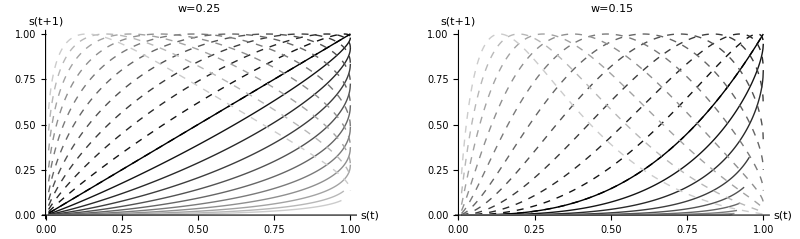

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

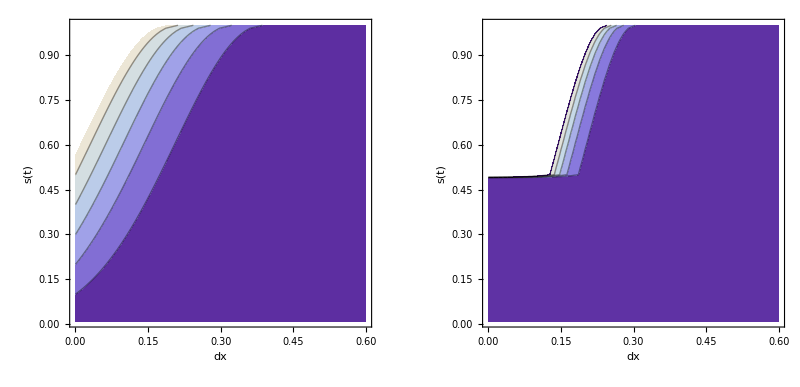

```mathematica
(* Find the positions where the Gaussian takes on values 0.1,..,1, only right side *)
positions=Table[FindRoot[Gaus[x,1.0,0.25]==val,{x,0.001,0,1}],{val,0.01,1,0.001}] ;
positions=x/.%;

(* Now move a certain amount away from these positions and find new values of Gaussian *)
PlotSMC[h_,w_,mv_,col_:0]:=Show[
ListLinePlot[Transpose[{Range[0.01,1,0.001],Gaus[positions+mv,h,w]}],PlotStyle->GrayLevel[col],AxesLabel->{"s(t)","s(t+1)"}],
ListLinePlot[Transpose[{Range[0.01,1,0.001],Gaus[-positions+mv,h,w]}],PlotStyle->{GrayLevel[col],Dashed}],
PlotRange->All
];

moves=Range[0.0,0.5,0.5/10];
wideSMC=Show[Table[PlotSMC[1,0.25,move,0.8*(move/Max[moves])],{move,moves}],PlotLabel->"w=0.25"];
narrowSMC=Show[Table[PlotSMC[1,0.15,move,0.8*(move/Max[moves])],{move,moves}],PlotLabel->"w=0.15"];
GraphicsRow[{wideSMC,narrowSMC}]

GausPos[y_,h_,w_]:=FindRoot[Gaus[x,h,w]==y,{x,0.001,0,1}] [[1,2]];
density =Table[Gaus[GausPos[val,1,0.18]+mv,1.0,0.18],{val,0.01,1,0.01},{mv,0,0.6,0.01}];
density2 =Table[Gaus[GausPos[val,1,0.1]+mv,1.0,0.1],{val,0.01,1,0.01},{mv,0,0.6,0.01}];
GraphicsRow[{ListContourPlot[density,FrameLabel->{"dx","s(t)"},DataRange->{{0,0.6},{0.01,1}}],ListContourPlot[density2,FrameLabel->{"dx","s(t)"},DataRange->{{0,0.6},{0.01,1}}]}]
(*GraphicsRow[{ListPlot3D[density,AxesLabel->{"s(t)","dx"},DataRange->{{0.01,1},{0,0.6}}],ListPlot3D[density2,AxesLabel->{"s(t)","dx"}]}]*)
```

### SMC with derivative sensor

#### Change in sensor value

```mathematica
(* Underlying sensor surface for all possible moves  *)
smcDx3d=Plot3D[(GausDx[x+dx,hh,ww]-GausDx[x,hh,ww])/1,{x,xmin,xmax},{dx,dxmin,dxmax},AxesLabel->{"x","dx"},ColorFunction->(ColorData["DarkRainbow"][#3]&),MeshFunctions->{#3&},Mesh->10,PlotRange->{{xmin,xmax},Automatic,All}];

smcDx3dAv=Plot3D[(GausDx[x+dx,hh,0.08]-GausDx[x,hh,0.08])/1,{x,-0.2,0.2},{dx,-0.004,0.004},AxesLabel->{"x","dx"},ColorFunction->(ColorData["DarkRainbow"][#3]&),MeshFunctions->{#3&},Mesh->10,PlotRange->{{-0.2,0.2},Automatic,All}];


smcDxCtr=ContourPlot[(GausDx[x+dx,hh,ww]-GausDx[x,hh,ww])/1,{x,xmin,xmax},{dx,dxmin,dxmax},ContourLabels->True,FrameLabel->{"x","dx"},PlotRange->{Automatic,Automatic,All}];

smcDxCtrAv=ContourPlot[(GausDx[x+dx,hh,0.08]-GausDx[x,hh,0.08])/1,{x,-0.2,0.2},{dx,dxmin,dxmax},ContourLabels->True,FrameLabel->{"x","dx"},PlotRange->{Automatic,Automatic,All}];


(* Overlay actual trajectories *)
sTr=GausDx[posTr,hh,ww];
sDx=GausDx[posTr+posDtTr,hh,ww]-sTr + 0.002;
catchSMCtrajX3d=Transpose[{posTr,posDtTr,sDx}];
catchSMCtrajX2d=Transpose[{posTr,posDtTr}];
catchSMCtrajS3d=Transpose[{posDtTr,sTr,sDx}];
catchSMCtrajXPl3d=Graphics3D[{Thick,Line[catchSMCtrajX3d,VertexColors->1-Range[0,1,1/(in-i0)]]},Axes->True,BoxRatios->1.0];
catchSMCtrajXPl2d=Graphics[{Thick,Line[catchSMCtrajX2d,VertexColors->1-Range[0,1,1/(in-i0)]]},Axes->True];
catchSMCtrajSPl3d=Graphics3D[{Thick,Line[catchSMCtrajS3d,VertexColors->1-Range[0,1,1/(in-i0)]]},Axes->True];

sTrAv=GausDx[posTrAv,hh,0.08];
sDxAv=GausDx[posTrAv+posDtTrAv,hh,0.08]-sTrAv + 0.002;
avoidSMCtrajX3d=Transpose[{posTrAv,posDtTrAv,sDxAv}];
avoidSMCtrajX2d=Transpose[{posTrAv,posDtTrAv}];
avoidSMCtrajS3d=Transpose[{posDtTrAv,sTrAv,sDxAv}];
avoidSMCtrajXPl3d=Graphics3D[{Thick,Line[avoidSMCtrajX3d,VertexColors->1-Range[0,1,1/(in-i0)]]},Axes->True,BoxRatios->1.0];
avoidSMCtrajXPl2d=Graphics[{Thick,Line[avoidSMCtrajX2d,VertexColors->1-Range[0,1,1/(in-i0)]]},Axes->True];
avoidSMCtrajSPl3d=Graphics3D[{Thick,Line[avoidSMCtrajS3d,VertexColors->1-Range[0,1,1/(in-i0)]]},Axes->True];

GraphicsGrid[{
{Show[smcDx3d,catchSMCtrajXPl3d],Show[smcDx3dAv,avoidSMCtrajXPl3d]},
{Show[smcDxCtr,catchSMCtrajXPl2d],Show[smcDxCtrAv,avoidSMCtrajXPl2d]}
},ImageSize->800]

(*Rasterize[%,ImageResolution->200]*)

maxSlope=GausDx[-ww,hh,ww] (* Max slope is exactly at w *)
maxSlopeAv=GausDx[-0.08,hh,0.08] (* Max slope is exactly at w *)
maxDiff=2 maxSlope;  (* Because of symmetry *)
```

-Graphics-

2.6283

0.985612

```mathematica
opacity=0.9;
smcDxDs3dInnerPos=Plot3D[GausDx[GausDxPosInner[y,hh,ww]+dx,hh,ww]-y,{dx,dxmin,dxmax},{y,-0.001,-maxSlope},AxesLabel->{"dx","s","ds"},MeshFunctions->{#3&},Mesh->None,PlotStyle->{colP,Opacity[1.0],Specularity[White,specul]}];
smcDxDs3dInnerNeg=Plot3D[-y+GausDx[-GausDxPosInner[-y,hh,ww]+dx,hh,ww],{dx,dxmin,dxmax},{y,0.001,maxSlope},AxesLabel->{"dx","s","ds"},MeshFunctions->{#3&},Mesh->None,PlotStyle->{colP,Opacity[1.0],Specularity[White,specul]}];
smcDxDs3dInner=Show[smcDxDs3dInnerPos,smcDxDs3dInnerNeg,PlotRange->All];

smcDxDs3dOuterPos=Plot3D[-y+GausDx[GausDxPosOuter[y,hh,ww]+dx,hh,ww],{dx,dxmin,dxmax},{y,-0.001,-maxSlope},AxesLabel->{"dx","s","ds"},MeshFunctions->{#3&},Mesh->None,PlotStyle->{colN,Opacity[0.3],Specularity[White,specul]}];
smcDxDs3dOuterNeg=Plot3D[-y+GausDx[-GausDxPosOuter[-y,hh,ww]+dx,hh,ww],{dx,dxmin,dxmax},{y,0.001,maxSlope},AxesLabel->{"dx","s","ds"},MeshFunctions->{#3&},Mesh->None,PlotStyle->{colN,Opacity[0.3],Specularity[White,specul]}];
smcDxDs3dOuter=Show[smcDxDs3dOuterPos,smcDxDs3dOuterNeg,PlotRange->All];

ww=0.08;
smcDxDs3dInnerPosAv=Plot3D[GausDx[GausDxPosInner[y,hh,ww]+dx,hh,ww]-y,{dx,dxmin,dxmax},{y,-0.001,-maxSlopeAv},AxesLabel->{"dx","s","ds"},MeshFunctions->{#3&},Mesh->None,PlotStyle->{colP,Opacity[0.75],Specularity[White,specul]}];
smcDxDs3dInnerNegAv=Plot3D[-y+GausDx[-GausDxPosInner[-y,hh,ww]+dx,hh,ww],{dx,dxmin,dxmax},{y,0.001,maxSlopeAv},AxesLabel->{"dx","s","ds"},MeshFunctions->{#3&},Mesh->None,PlotStyle->{colP,Opacity[0.75],Specularity[White,specul]}];
smcDxDs3dInnerAv=Show[smcDxDs3dInnerPosAv,smcDxDs3dInnerNegAv,PlotRange->All];

smcDxDs3dOuterPosAv=Plot3D[-y+GausDx[GausDxPosOuter[y,hh,ww]+dx,hh,ww],{dx,dxmin,dxmax},{y,-0.001,-maxSlopeAv},AxesLabel->{"dx","s","ds"},MeshFunctions->{#3&},Mesh->None,PlotStyle->{colN,Opacity[0.3],Specularity[White,specul]}];
smcDxDs3dOuterNegAv=Plot3D[-y+GausDx[-GausDxPosOuter[-y,hh,ww]+dx,hh,ww],{dx,dxmin,dxmax},{y,0.001,maxSlopeAv},AxesLabel->{"dx","s","ds"},MeshFunctions->{#3&},Mesh->None,PlotStyle->{colN,Opacity[0.3],Specularity[White,specul]}];
smcDxDs3dOuterAv=Show[smcDxDs3dOuterPosAv,smcDxDs3dOuterNegAv,PlotRange->All];
ww=0.03;


test=GraphicsGrid[{
{Show[smcDxDs3dInnerAv,avoidSMCtrajSPl3d,PlotRange->{{dxmin,dxmax},All,All}],Show[smcDxDs3dOuterAv,avoidSMCtrajSPl3d,PlotRange->{{dxmin,dxmax},All,All}]},
{Show[smcDxDs3dInnerAv,smcDxDs3dOuterAv,avoidSMCtrajSPl3d,PlotRange->{{dxmin,dxmax},All,All}],SpanFromLeft}
},ImageSize->800]


test=GraphicsGrid[{
{Show[smcDxDs3dInner,catchSMCtrajSPl3d],Show[smcDxDs3dOuter,catchSMCtrajSPl3d]},
{Show[smcDxDs3dInner,smcDxDs3dOuter,catchSMCtrajSPl3d],SpanFromLeft}
},ImageSize->800]

(*Rasterize[test,ImageResolution->200]*)
```

-Graphics-

-Graphics-

#### Next sensor value map

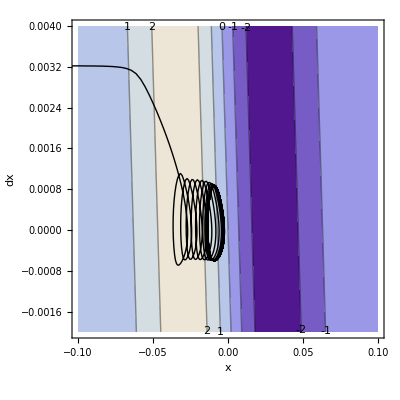

```mathematica
smcDx3d=Plot3D[GausDx[x+dx,hh,ww],{x,xmin,xmax},{dx,dxmin,dxmax},AxesLabel->{"x","dx"},ColorFunction->(ColorData["DarkRainbow"][#3]&),MeshFunctions->{#3&},Mesh->5];

smcDxCtr=ContourPlot[GausDx[x+dx,hh,ww],{x,xmin,xmax},{dx,dxmin,dxmax},ContourLabels->True,FrameLabel->{"x","dx"}];

ssdx=GausDx[posTr+posDtTr,hh,ww];
catchSMCtrajX3dSS=Transpose[{posTr,posDtTr,ssdx}];
catchSMCtrajX2dSS=Transpose[{posTr,posDtTr}];
catchSMCtrajX3dSSPl =Graphics3D[{Thick,Line[catchSMCtrajX3dSS,VertexColors->1-Range[0,1,1/(in-i0)]]},Axes->True,BoxRatios->1.0];
catchSMCtrajX2dSSPl =Graphics[{Thick,Line[catchSMCtrajX2dSS,VertexColors->1-Range[0,1,1/(in-i0)]]},Axes->True];
GraphicsRow[{Show[smcDx3d,catchSMCtrajX3dSSPl],Show[smcDxCtr,catchSMCtrajX2dSSPl]},ImageSize->800]

(*Rasterize[%,ImageResolution->200]*)
```

Same as absolute sensor. This is the same as shifting the derivative of the gaussian by dx.

```mathematica
catchSMCtrajS3dSS=Transpose[{posDtTr,sTr,ssdx}];
catchSMCtrajS3dSSPl =Graphics3D[{Thick,Line[catchSMCtrajS3dSS,VertexColors->1-Range[0,1,1/(in-i0)]]},Axes->True,BoxRatios->1.0];

smcDxSS3dInnerPos=Plot3D[GausDx[GausDxPosInner[y,hh,ww]+dx,hh,ww],{dx,dxmin,dxmax},{y,-0.001,-maxSlope},AxesLabel->{"dx","ds"},MeshFunctions->{#3&},Mesh->None,PlotStyle->{colP,Opacity[1],Specularity[White,specul]}];

smcDxSS3dInnerNeg=Plot3D[GausDx[-GausDxPosInner[-y,hh,ww]+dx,hh,ww],{dx,dxmin,dxmax},{y,0.001,maxSlope},AxesLabel->{"dx","ds"},MeshFunctions->{#3&},Mesh->None,PlotStyle->{colP,Opacity[1],Specularity[White,specul]}];

smcDxSS3dInner=Show[smcDxSS3dInnerPos,smcDxSS3dInnerNeg,PlotRange->All];

smcDxSS3dOuterPos=Plot3D[GausDx[GausDxPosOuter[y,hh,ww]+dx,hh,ww],{dx,dxmin,dxmax},{y,-0.001,-maxSlope},AxesLabel->{"dx","ds"},MeshFunctions->{#3&},Mesh->None,PlotStyle->{colN,Opacity[0.3],Specularity[White,specul]}];

smcDxSS3dOuterNeg=Plot3D[GausDx[-GausDxPosOuter[-y,hh,ww]+dx,hh,ww],{dx,dxmin,dxmax},{y,0.001,maxSlope},AxesLabel->{"dx","ds"},MeshFunctions->{#3&},Mesh->None,PlotStyle->{colN,Opacity[0.3],Specularity[White,specul]}];

smcDxSS3dOuter=Show[smcDxSS3dOuterPos,smcDxSS3dOuterNeg,PlotRange->All];

GraphicsGrid[{
{Show[smcDxSS3dInner,catchSMCtrajS3dSSPl],Show[smcDxSS3dOuter,catchSMCtrajS3dSSPl]},
{Show[smcDxSS3dInner,smcDxSS3dOuter,catchSMCtrajS3dSSPl],SpanFromLeft}
},ImageSize->800]

(*Rasterize[%,ImageResolution->200]*)
```

-Graphics-

## Fitness

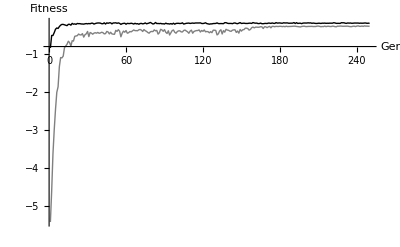

-0.163453

```mathematica
bestFitP =ListLinePlot[bestFitness,PlotStyle->Black,PlotRange->All,ImageSize->400,AxesLabel->{Gen, Fitness}];
avgFitP =ListLinePlot[avgFitness,PlotStyle->Gray,PlotRange->All,ImageSize->400];
Show[bestFitP, avgFitP]
maxFit = Max[bestFitness]
```

## Generalization

Fitness (distance from center of Gaussian) as a function of the height (horizontal) and width (vertical) of the Gaussian. Only one Gaussian was presented in these trials. For each combination of width and height, the Gaussian was presented at 10 locations, uniformly distributed over the horizontal field of view (-0.4, 0.4) and at a distance of 0.4 (the maximum sensor distance). During evolution only two widths were encountered: 0.03 and 0.08, while the amplitude varied around 0.13 +- 50%.

```mathematica
slopes2d=Abs[Table[GausDx[HWHM[width],height,width],{height,heightRange},{width,widthRange}]];
maxSlope=Round[Max[slopes2d],0.01];
minSlope=Round[Min[slopes2d],0.01];
color="GrayTones";

slopeDensity=DensityPlot[Abs[GausDx[width,height,width]],{height,Min[heightRange],Max[heightRange]},{width,Min[widthRange],Max[widthRange]},ColorFunction->ColorData[color],FrameLabel->Automatic];

slopeContours=ContourPlot[Abs[GausDx[width,height,width]],{height,Min[heightRange],Max[heightRange]},{width,Min[widthRange],Max[widthRange]},ContourShading->None,Contours->8,(*ContourStyle->Directive[Black,Dashed],*)ColorFunction->ColorData[color],FrameLabel->Automatic];

slopeCombined=Show[slopeDensity,slopeContours];

slopeDensityPlot=With[{size=225},Row[Show[#,ImageSize->{Automatic,size},ImagePadding->{{25,5},{20,5}}]&/@{slopeCombined,Colorbar[ColorData[color],minSlope,maxSlope,10]}]];

genFitMin=Round[Min[genFit],0.001];
genFitMax=Round[Max[genFit],0.001];
numContours=10;
```

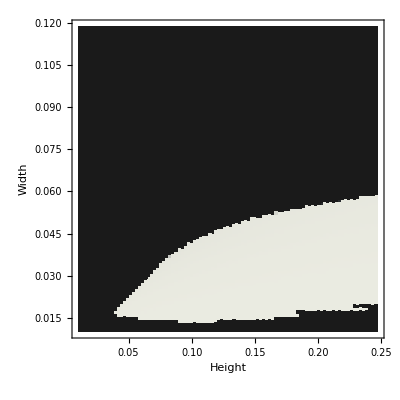
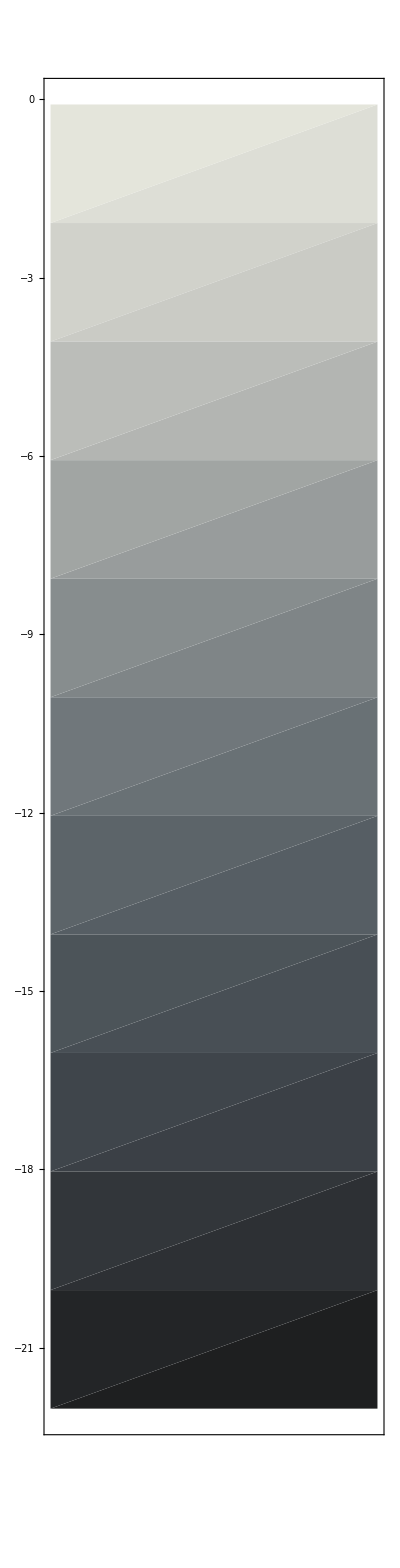
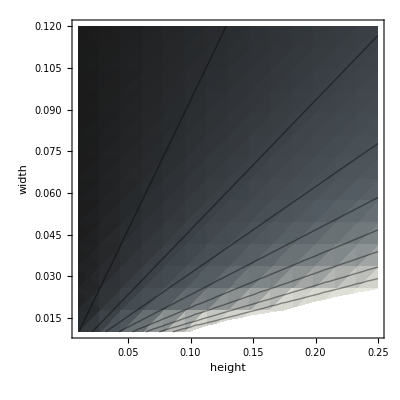
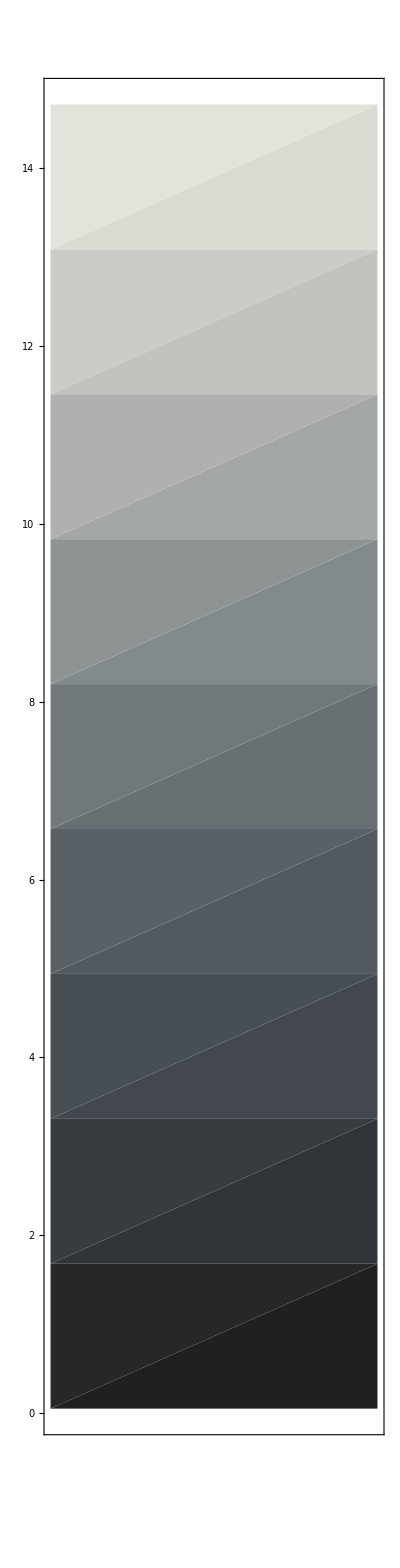

```mathematica
fitdens=ListDensityPlot[genFit,DataRange->{{0.01,0.2476},{0.01,0.1189}},ColorFunction->ColorData[color],ColorFunctionScaling->True,InterpolationOrder->0,FrameLabel->{"Height","Width"}];

fitDensityPlot=With[{size=225},Row[Show[#,ImageSize->{Automatic,size},ImagePadding->{{25,5},{20,5}}]&/@{fitdens,Colorbar[ColorData[color],genFitMin,genFitMax,12]}]];

fitDensityPlot slopeDensityPlot
```

The fitness density plot resembles features of the slope density plot.

```mathematica
(*
colbar=Colorbar[ColorData[color],genFitMin, genFitMax,12];
colbar=Show[colbar,ImagePadding->{{25,5},{20,5}},ImageSize->ImageDimensions[fitDensityPlot[[1,2]]]];
colbar2=Colorbar[ColorData[color],minSlope, maxSlope,12];
colbar2=Show[colbar2,ImagePadding->{{25,5},{20,5}},ImageSize->ImageDimensions[fitDensityPlot[[1,2]]]];

barOpt=Options[Graphics[{},AlignmentPoint->Center,AspectRatio->10,Axes->False,AxesLabel->None,BaseStyle->{FontFamily->"Arial",FontSize->12},Frame->True,FrameStyle->Directive[Black],FrameTicks->{None,Automatic,None,None},FrameTicksStyle->Directive[10,Black],ImagePadding->{{25,5},{20,5}},LabelStyle->Directive[Black],PlotRangeClipping->True,PlotRangePadding->Scaled[0.0]]];

Rastered[fitDensityPlot[[1,1]],figExpPath<>"GenFit",ImageDimensions[fitDensityPlot[[1,1]]],Options[G2D2]]
Rastered[colbar,figExpPath<>"GenFitColBar",ImageDimensions[fitDensityPlot[[1,2]]],barOpt]

Rastered[slopeDensityPlot[[1,1]],figExpPath<>"GenSlope",ImageDimensions[slopeDensityPlot[[1,1]]],Options[G2D2]]
Rastered[colbar2,figExpPath<>"GenSlopeColBar",ImageDimensions[slopeDensityPlot[[1,2]]],barOpt]
*)
```

## Time series

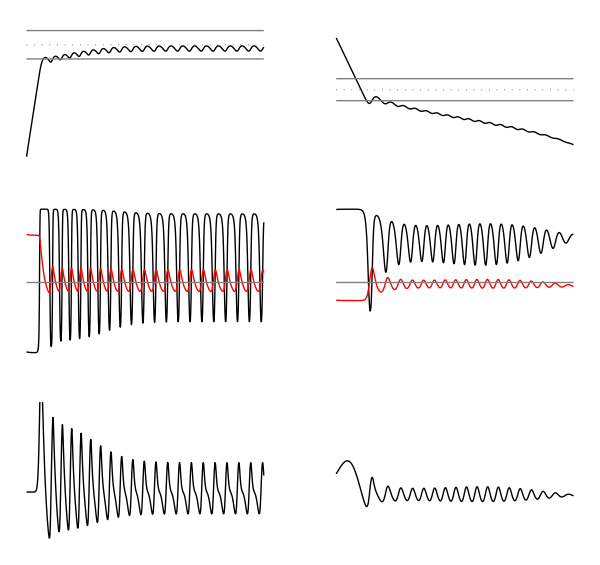

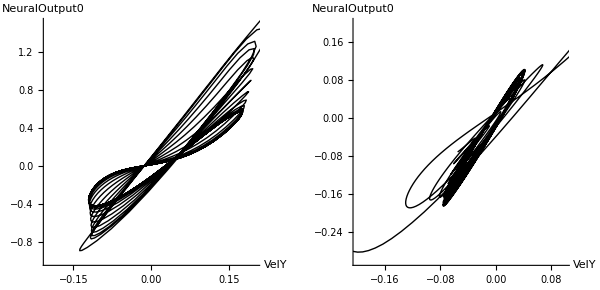

```mathematica
T=10.0; (* trial duration in seconds *)
startAt=0.0;
duration=5.0;
trials={2,12};
SetStartEnd[tr_]:={i0,in}={1+TtoI[trials[[tr]]*T+startAt],TtoI[trials[[tr]]*T+startAt+duration]};

neuralPlotRange={Automatic,{0,1}};
sensorPlotRange={Automatic,{-1.1,1.75}};
posPlotRange2={Automatic,{-0.1,0.3}};

AllMaxima[lst_]:=Flatten[Position[Partition[Differences[lst],2,1],{x_,y_}/;Sign[x]>Sign[y]]];
AllMinima[lst_]:=Flatten[Position[Partition[Differences[lst],2,1],{x_,y_}/;Sign[x]<Sign[y]]];
ThreshMax[lst_,t_]:=Cases[AllMaxima[lst]+1,x_/;lst[[x]]>t];
ThreshMin[lst_,t_]:=Cases[AllMaxima[lst]+1,x_/;lst[[x]]<t];

(* First trial *)
infl=0.03;
SetStartEnd[1];
options={PlotStyle->Black,Frame->{{Automatic,None},{Automatic,None}},Axes->None,PlotRangePadding->None};
posP=Show[TimePlot["PosY",i0,in,{options,PlotRange->{Automatic,{-0.25,2*infl}}}]];
centre=ListLinePlot[{{0,0},{(in-i0)*dt,0}},PlotStyle->{Gray,Dotted}];
infl1=ListLinePlot[{{0,infl},{(in-i0)*dt,infl}},PlotStyle->{Gray}];
infl2=ListLinePlot[{{0,-infl},{(in-i0)*dt,-infl}},PlotStyle->{Gray}];
posP=Show[posP,infl1, infl2,centre];
hiddenP=Show[TimePlot["NeuralOutput1",i0,in,{options,PlotRange->neuralPlotRange}]];
outputP=Show[TimePlot["NeuralOutput2",i0,in,Join[{PlotStyle->Red},options]]];
midLine=ListLinePlot[{{0,0.5},{(in-i0)*dt,0.5}},PlotStyle->{Gray}];
hiddenOutputP=Show[hiddenP,outputP,midLine];
sensorP=Show[TimePlot["NeuralOutput0",i0,in,{options,PlotRange->sensorPlotRange}]];


velInPhPlot = PhasePlot["VelY","NeuralOutput0",i0,in,{PlotRange->{{-0.2,0.2},{-1.0,1.5}},AspectRatio->1}];

(* Another trial for comparison *)
startAt=4.5;
duration=5.5;
SetStartEnd[2];
posP2=Show[TimePlot["PosY",i0,in,{options,PlotRange->{Automatic,{-0.2,0.2}}}]];
centre=ListLinePlot[{{0,0},{(in-i0)*dt,0}},PlotStyle->{Gray,Dotted}];
infl1=ListLinePlot[{{0,infl},{(in-i0)*dt,infl}},PlotStyle->{Gray}];
infl2=ListLinePlot[{{0,-infl},{(in-i0)*dt,-infl}},PlotStyle->{Gray}];
posP2=Show[posP2,infl1, infl2,centre];
hiddenP2=Show[TimePlot["NeuralOutput1",i0,in,{options,PlotRange->neuralPlotRange}]];
outputP2=Show[TimePlot["NeuralOutput2",i0,in,Join[{PlotStyle->Red},options]]];
midLine=ListLinePlot[{{0,0.5},{(in-i0)*dt,0.5}},PlotStyle->{Gray}];
hiddenOutputP2=Show[hiddenP2,outputP2,midLine];
sensorP2=Show[TimePlot["NeuralOutput0",i0,in,{options,PlotRange->sensorPlotRange}]];

velInPhPlot2 = PhasePlot["VelY","NeuralOutput0",i0,in,{PlotRange->{{-0.2,0.1},{-0.3,0.2}},AspectRatio->1}];

g=GraphicsGrid[{{posP,posP2},{hiddenOutputP,hiddenOutputP2},{sensorP,sensorP2}}, ImageSize->600]
(*Rasterize[%,ImageResolution->200]*)
(*Export["exportPdf/TimeSeries.eps",g];*)

GraphicsGrid[{{velInPhPlot,velInPhPlot2}},ImageSize->600]
(*Rasterize[%,ImageResolution->200]*)

(*
(* All catching trajectories from different starting positions *)
PlotPosTrial[tr_]:=TimePlot["PosY",1+TtoI[tr*T+startAt],1+TtoI[tr*T+startAt+duration],{PlotStyle->GrayLevel[Mod[tr,10]/10],PlotRange->{All,{-0.5,0.5}}}]

startAt=0;
duration=9.9;
all1=Show[Table[PlotPosTrial[i],{i,0,4}]];
all2=Show[Table[PlotPosTrial[i],{i,10,14}]];
Show[all1,all2]
*)
```

### SMC: change in perception as function of change in motor command

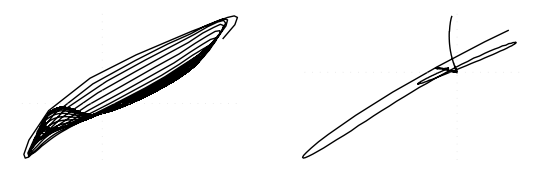

```mathematica
startAt=0.5;
duration=9.5;
SetStartEnd[1];
perceptDt=Differences[NtoD["NeuralOutput0",i0,in]];
motorDt=Differences[NtoD["NeuralOutput2",i0,in]]*100;
catchSMCtraj=Transpose[{motorDt,perceptDt}];

options={Frame->{{Automatic,None},{Automatic,None}},Axes->None,AspectRatio->1/1.5,GridLines->{{0},{0}},GridLinesStyle->Dotted,ImagePadding->{{50,0},{35,0}}};
catchSMC=Graphics[Line[catchSMCtraj,VertexColors->0.8-Range[0,0.8,0.8/(in-i0)]](*,PlotRange->{{-0.009,0.014},{-0.08,0.13}}*),FrameLabel->{"dm/dt  [x10^-2]","ds/dt"},options,Options[G2D2]];

catchTimePlot=Show[ListLinePlot[perceptDt,PlotStyle->Black],ListLinePlot[10*motorDt,PlotStyle->{Black,Dashed}],FrameLabel->{"time","s', m'"}];

startAt=0.5;
duration=4.0;
SetStartEnd[2];
perceptDt=Differences[NtoD["NeuralOutput0",i0,in]]*100;
motorDt=Differences[NtoD["NeuralOutput2",i0,in]]*100;
catchSMCtraj=Transpose[{motorDt,perceptDt}];

avoidSMC=Graphics[Line[catchSMCtraj,VertexColors->0.8-Range[0,0.8,0.8/(in-i0)]](*,PlotRange->{{-0.009,0.014},{-0.08,0.13}}*),FrameLabel->{"dm/dt [x10^-2]","ds/dt [x10^-2]"},options,Options[G2D2]];

avoidTimePlot=Show[ListLinePlot[perceptDt,PlotStyle->Black,PlotRange->Automatic],ListLinePlot[motorDt,PlotStyle->{Black,Dashed}],AxesLabel->{"time","s', m'"}];

g1=GraphicsRow[{catchSMC,avoidSMC},ImageSize->72 7.5]
Export[figExpPath<>"SMCoordPattern.eps",g1];

(*Rasterize[%,ImageResolution->200]*)

(*GraphicsRow[{catchTimePlot,avoidTimePlot}]*)
```

Feature: In the catching case, in some region m’ is already positive even though s’ reverses direction for a short amount of time. Presumably, this is because m’ is determined by the motor neuron, which via the hidden neuron, has bistable characteristics. Once a certain threshold (the basin boundary) has been crossed, m’ will move towards positive EP.

## Sensorimotor habitat

```mathematica
trial={{2,0.0,3.0},{10,0.0,2.5}};
Trial[tr_]:={i0,in}={1+TtoI[trial[[tr,1]]*T+trial[[tr,2]]],TtoI[trial[[tr,1]]*T+trial[[tr,2]]+trial[[tr,3]]]};

Trial[1];
ww=0.03;hh=0.13;www=0.08;
Sensed[x_,h_,w_]:= 1-((0.4-Gaus[x,h,w])/0.4);

(* Plot catch sensorimotor environment *)
posCatch = NtoD["PosY",i0,in];
speedCatch=NtoD["VelY",i0,in];

distClc=Sensed[pos,hh,ww];
distRec=NtoD["Sensor",i0,in];
Show[ListLinePlot[distClc],ListLinePlot[distRec] ]; (* Make sure we're correctly reconstructing the measured distance and sensor derivative *)

sensedClc=(Sensed[pos+speedCatch*dt,hh,ww]-Sensed[pos,hh,ww])/dt;
sensedRecCatch=NtoD["SensorDer",i0,in]+0.4;
Show[ListLinePlot[sensedClc],ListLinePlot[sensedRecCatch]];

sensedInput3dCatch=Plot3D[(Sensed[xt+vt*dt,hh,ww]-Sensed[xt,hh,ww])/dt,{xt,-5*ww,5*ww},{vt,-0.5,0.75},PlotRange->All,AxesLabel->{"x","v","s"}];

sensedInputTrjCatch=Graphics3D[{Thick,Line[Transpose[{pos,speedCatch,sensedRecCatch}],VertexColors->0.9-Range[0,0.9,0.9/(in-i0)]]},Axes->True,BoxRatios->1,PlotRange->{{-5ww,5ww},{-0.5,0.75},All}];

sensedInCatch=Show[sensedInput3dCatch,sensedInputTrjCatch,PlotRange->{{-5ww,5ww},{-0.5,0.75},All}];

(* Plot avoid sensorimotor environment *)
Trial[2];
posAvoid = NtoD["PosY",i0,in];
speedAvoid=NtoD["VelY",i0,in];
sensedRecAvoid=NtoD["SensorDer",i0,in]+0.1;

sensedInput3dAvoid=Plot3D[(Sensed[xt+vt*dt,hh,www]-Sensed[xt,hh,www])/dt,{xt,-5*www,5*www},{vt,-0.5,0.75},PlotRange->All,AxesLabel->{"x","v","s"}];

sensedInputTrjAvoid=Graphics3D[{Thick,Line[Transpose[{posAvoid,speedAvoid,sensedRecAvoid}],VertexColors->0.9-Range[0,0.9,0.9/(in-i0)]]},Axes->True,BoxRatios->1,PlotRange->{{-5www,5www},{-0.5,0.75},All}];

sensedInAvoid=Show[sensedInput3dAvoid,sensedInputTrjAvoid,PlotRange->{{-5www,5www},{-0.5,0.75},All}];

(*GraphicsRow[{sensedInCatch,sensedInAvoid},ImageSize->800]*)
```

ListLinePlot::lpn: 1 - 2.5\ (0.4  - 0.13\ ⅇ^-555.556\ pos^2)
 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ListLinePlot[1 - 2.5` (0.4`  - 0.13` ⅇ^Times[« 2 »])], GraphicsBox[List[List[List[], List[], List[Hue[0.67`, 0.6`, 0.6`], LineBox[List[List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], Skeleton[550]]]]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[List[0.`, 600.`], List[0.`, 0.323743`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Scaled[0.02`], Scaled[0.02`]]]]]
.

Transpose::nmtx: The first two levels of the one-dimensional list {pos, {« 1 »}, {0.4, 0.4, 0.4, 0.4, 0.4, 0.4, 0.4, 0.4, 0.4, 0.4, 0.4, 0.4, 0.4, 0.4, 0.4, 0.4, 0.4, 0.4, 0.4, 0.4, 0.4, 0.4, 0.400012, 0.4, 0.400012, 0.400036, 0.400024, 0.400083, 0.400119, 0.400191, 0.400322, 0.400525, 0.400846, 0.401359, 0.402122, 0.403302, 0.405054, 0.407641, 0.411444, 0.416928, 0.424676, 0.435584, 0.450664, 0.471228, 0.498896, 0.535577, 0.583475, 0.64519, 0.723331, 0.820868, « 550 »}} cannot be transposed.

### Calculate EPs (takes a long time ! )

```mathematica
EPInBi[inputVal_]:=Module[{eps,ep},
eps=EquilibriumPoints[network/.J->inputVal,Tries->100,MaxIterations->50];
ep=If[Length[eps]==1,eps[[1,3,2]],  -1];
ep
];

sensedInputTblCatch=Table[(Sensed[xt+vt*dt,hh,ww]-Sensed[xt,hh,ww])/dt,{xt,-0.3,0.3,0.01},{vt,-0.5,0.75,0.05}];
sensedInputTblAvoid=Table[(Sensed[xt+vt*dt,hh,www]-Sensed[xt,hh,www])/dt,{xt,-0.3,0.3,0.01},{vt,-0.5,0.75,0.05}];

Dimensions[sensedInputTblCatch]
epTblBiCatch=Map[EPInBi,sensedInputTblCatch*inW,{2}];
Dimensions[epTblBiCatch]
epTblBiAvoid=Map[EPInBi,sensedInputTblAvoid*inW,{2}];
```

{61,26}

{61,26}

```mathematica
EPforIn[inputVal_,hidOut_]:=Module[{eps,ep},
eps=EquilibriumPoints[network/.J->inputVal,Tries->200,MaxIterations->50];
ep=If[Length[eps]==1,eps[[1,3,2]], If[hidOut<eps[[2,3,1]],eps[[1,3,2]],eps[[3,3,2]] ]];
ep
];

Trial[1];
sensorCatchTraj=NtoD["NeuralOutput0",i0,in]*inW;
hiddenStateCatchTraj=NtoD["NeuralState1",i0,in];
hiddenCatchTraj=NtoD["NeuralOutput1",i0,in];
motorEPCatch=Table[EPforIn[sensorCatchTraj[[i]],hiddenStateCatchTraj[[i]]],{i,1,Length[hiddenCatchTraj],5}];

Trial[2];
sensorAvoidTraj=NtoD["NeuralOutput0",i0,in]*inW;
hiddenStateAvoidTraj=NtoD["NeuralState1",i0,in];
hiddenAvoidTraj=NtoD["NeuralOutput1",i0,in];
motorEPAvoid=Table[EPforIn[sensorAvoidTraj[[i]],hiddenStateAvoidTraj[[i]]],{i,1,Length[hiddenAvoidTraj],5}];
```

Part::partw: Part 3 of {"EquilibriumPoint[Stable,Node,\!\({\(\(-0.32687\)\), \(\(-0.0269402\)\)}\)]", "EquilibriumPoint[Stable,Node,\!\({6.59309, \(\(-1.93278\)\)}\)]"} does not exist.

### Convert to EP surfaces

-Graphics-

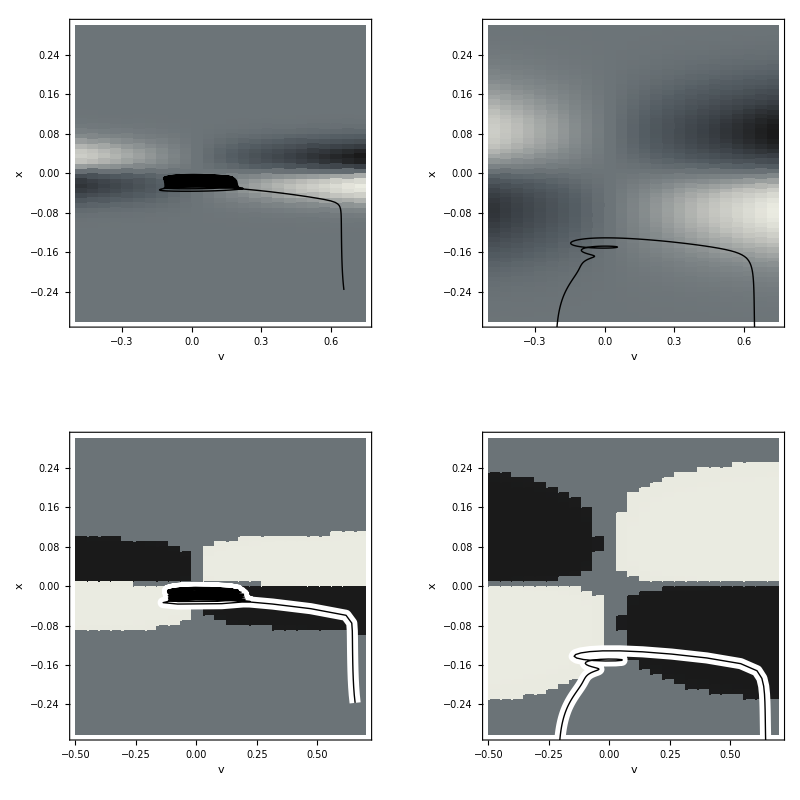

```mathematica
(* Transform state EPs into output EPs *)
epTblBiCatchRpl=σ[epTblBiCatch+1.57389];
epTblBiAvoidRpl=σ[epTblBiAvoid+1.57389];
motorEPCatchRpl=σ[motorEPCatch+1.57389];
motorEPAvoidRpl=σ[motorEPAvoid+1.57389];

(* Move plane of bistability to middle of attractors for aesthetic reasons *)
epTblBiCatchRpl=ReplaceAll[epTblBiCatchRpl,(x_/;Abs[x-0.63966]<0.001)->0.6];
epTblBiAvoidRpl=ReplaceAll[epTblBiAvoidRpl,(x_/;Abs[x-0.63966]<0.001)->0.6];


(* Map output neuron EPs to velocties *)
(*epTblBiCatch=2*epTblBiCatch-1;
epTblBiAvoid=2*epTblBiAvoid-1;*)

(* First, the sensed input as function of motor action (sensorimotor environment) *)
(* 3D *)
cam={-2,-1,1};
colScheme="GrayTones";
light={{"Ambient",RGBColor[{0.35,0.35,0.35}]},
{"Directional",RGBColor[{0.17,0.17,0.17}],ImageScaled[{2,0,2}]},{"Directional",RGBColor[{0.27,0.27,0.27}],ImageScaled[{2,2,2}]},{"Directional",RGBColor[{0.37,0.37,0.37}],ImageScaled[{0,2,2}]}};

sensedInputCatch3d=ListPlot3D[sensedInputTblCatch,PlotRange->All,ColorFunction->(ColorData[colScheme][#3]&),Lighting->light,Mesh->None,AxesLabel->{"v","x"},DataRange->{{-0.5,0.75},{-0.3,0.3},All},ViewPoint->cam,ImageSize->800];


sensedInputAvoid3d=ListPlot3D[sensedInputTblAvoid,ColorFunction->(ColorData[colScheme][#3]&),Lighting->light,Mesh->None,AxesLabel->{"v","x"},DataRange->{{-0.5,0.75},{-0.3,0.3}},PlotRange->{Automatic,Automatic,{-5,5}},ViewPoint->cam];

sensedInputTrjRevCatch=Graphics3D[{Thick,Line[Transpose[{speedCatch,posCatch,sensedRecCatch}],VertexColors->1-Range[0.0,0.9,0.9/(in-i0)]]},Axes->True,BoxRatios->1,PlotRange->{{-0.5,0.75},{-5ww,5ww},Automatic}];
sensedSMCatch=Show[sensedInputCatch3d,sensedInputTrjRevCatch,PlotRange->{{-0.5,0.75},{-5ww,5ww},All}];

sensedInputTrjRevAvoid=Graphics3D[{Thick,Line[Transpose[{speedAvoid,posAvoid,sensedRecAvoid}],VertexColors->1-Range[0.0,0.9,0.9/(in-i0)]]},Axes->True,BoxRatios->1,PlotRange->{{-0.5,0.75},{-5www,5www},Automatic}];
sensedSMAvoid=Show[sensedInputAvoid3d,sensedInputTrjRevAvoid,PlotRange->{{-0.5,0.75},{-5www,5www},All}];

(* 2D *)
sensedDensCatch=ListDensityPlot[sensedInputTblCatch,DataRange->{{-0.5,0.75},{-0.3,0.3}},PlotRange->All,ColorFunction->ColorData[colScheme],ColorFunctionScaling->True,InterpolationOrder->0,FrameLabel->{"v","x"}];
sensedDensAvoid=ListDensityPlot[sensedInputTblAvoid,DataRange->{{-0.5,0.75},{-0.3,0.3}},PlotRange->All,ColorFunction->ColorData[colScheme],ColorFunctionScaling->True,InterpolationOrder->0,FrameLabel->{"v","x"}];

sensedInputTrjRevCatch2d=Graphics[{Thick,Line[Transpose[{speedCatch,posCatch}],VertexColors->1-Range[0.0,0.9,0.9/(in-i0)]]},Axes->True,PlotRange->{{-0.5,0.75},{-0.3,0.3}}];
sensedSMCatch2d=Show[sensedDensCatch,sensedInputTrjRevCatch2d,PlotRange->{{-0.5,0.75},{-0.3,0.3}}];

sensedInputTrjRevAvoid2d=Graphics[{Thick,Line[Transpose[{speedAvoid,posAvoid}],VertexColors->1-Range[0.0,0.9,0.9/(in-i0)]]},Axes->True,PlotRange->{{-0.5,0.75},{-0.3,0.3}}];
sensedSMAvoid2d=Show[sensedDensAvoid,sensedInputTrjRevAvoid2d,PlotRange->{{-0.5,0.75},{-0.3,0.3}}];

(* Now, the the internal equilibria as function of sensed input (agential motorsensory habitat) *)
(* 3D *)
epTblBi3dCatch=ListPlot3D[epTblBiCatchRpl,PlotRange->All,ColorFunction->(ColorData[colScheme][#3]&),Mesh->None,PlotStyle->{Opacity[1]},AxesLabel->{"v","x"},DataRange->{{-0.5,0.75},{-0.3,0.3}},ViewPoint->cam,Lighting->light];

epTblBi3dAvoid=ListPlot3D[epTblBiAvoidRpl,PlotRange->All,RegionFunction->Function[{x,y,z},z≠0.0],ColorFunction->(ColorData[colScheme][#3]&),Mesh->None,AxesLabel->{"v","x"},DataRange->{{-0.5,0.75},{-0.3,0.3}},ViewPoint->cam,Lighting->light];

motorEPColsCatch=Map[If[#<0.6,ColorData[colScheme][0],ColorData[colScheme][1]]&,motorEPCatchRpl];
motorEPColsAvoid=Map[If[#<0.6,ColorData[colScheme][0],ColorData[colScheme][1]]&,motorEPAvoidRpl];

Trial[1];
outputTrj3dCatch=Graphics3D[{Thick,Line[Transpose[{speedCatch,posCatch,NtoD["NeuralOutput2",i0,in]}][[1;;-1;;5]],VertexColors->motorEPColsCatch]},Axes->True,BoxRatios->1,PlotRange->{{-0.5,0.75},{-5ww,5ww},All}];
Trial[2];
outputTrj3dAvoid=Graphics3D[{Thick,Line[Transpose[{speedAvoid,posAvoid,NtoD["NeuralOutput2",i0,in]}][[1;;-1;;5]],VertexColors->motorEPColsAvoid]},Axes->True,BoxRatios->1,PlotRange->{{-0.5,0.75},{-5www,5www},All}];

catchEP3d=Show[epTblBi3dCatch,outputTrj3dCatch,PlotRange->{{-0.5,0.75},{-5ww,5ww},All}];
avoidEP3d=Show[epTblBi3dAvoid,outputTrj3dAvoid,PlotRange->{{-0.5,0.75},{-5www,5www},All}];

(* 2D *)
epDensCatch=ListDensityPlot[epTblBiCatchRpl,RegionFunction->Function[{x,y,z},z≠0.0],DataRange->{{-0.5,0.7},{-0.3,0.3}},PlotRange->All,ColorFunction->ColorData[colScheme],ColorFunctionScaling->True,InterpolationOrder->0,FrameLabel->{"v","x"}];
epDensAvoid=ListDensityPlot[epTblBiAvoidRpl,RegionFunction->Function[{x,y,z},z≠0.0],DataRange->{{-0.5,0.7},{-0.3,0.3}},PlotRange->All,ColorFunction->ColorData[colScheme],ColorFunctionScaling->True,InterpolationOrder->0,FrameLabel->{"v","x"}];

outputTrj2dCatch=Graphics[{Thick,Line[Transpose[{speedCatch,posCatch}][[1;;-1;;5]],VertexColors->motorEPColsCatch]},Axes->True,PlotRange->{{-0.5,0.75},{-0.3,0.3}}];
outputTrj2dCatchBgr=Graphics[{Thickness[0.02],White,Line[Transpose[{speedCatch,posCatch}][[1;;-1;;5]]]},Axes->True,PlotRange->{{-0.5,0.75},{-0.3,0.3}}];
outputTrj2dAvoid=Graphics[{Thick,Line[Transpose[{speedAvoid,posAvoid}][[1;;-1;;5]],VertexColors->motorEPColsAvoid]},Axes->True,PlotRange->{{-0.5,0.75},{-0.3,0.3}}];
outputTrj2dAvoidBgr=Graphics[{Thickness[0.02],White,Line[Transpose[{speedAvoid,posAvoid}][[1;;-1;;5]]]},Axes->True,PlotRange->{{-0.5,0.75},{-0.3,0.3}}];

catchEP2d=Show[epDensCatch,outputTrj2dCatchBgr,outputTrj2dCatch,PlotRange->{{-0.5,0.7},{-0.3,0.3}}];
avoidEP2d=Show[epDensAvoid,outputTrj2dAvoidBgr,outputTrj2dAvoid,PlotRange->{{-0.5,0.7},{-0.3,0.3}}];

(* Show *)
size=800;
g1=GraphicsGrid[{{sensedInputCatch3d,sensedInputAvoid3d},{epTblBi3dCatch,epTblBi3dAvoid}},ImageSize->size]
g2=GraphicsGrid[{{sensedSMCatch2d,sensedSMAvoid2d},{catchEP2d,avoidEP2d}},ImageSize->size]




size=225;
(*
axes=Graphics[{},Background->None, FilterRules[AbsoluteOptions[g1],Except[FrameTicks]]]
fig=Show[g1,FrameStyle->Directive[Opacity[0]]];
fig=Magnify[fig,5];
fig=Rasterize[fig,"Image",Background->None];
fig=fig/.{255,255,255,255}->{0,0,0,0}
axes=First@ImportString[ExportString[axes,"PDF"],"PDF"];
result=Show[axes,Epilog->Inset[fig,{0,0},{0,0},ImageDimensions[axes]]]
Export["Result.eps",result,Background->None]
*)

(*
gr=Show[avoidEP2d,Options[G2D2]]
axes=Graphics[{},FilterRules[AbsoluteOptions[gr],Except[FrameTicks]]];
plot=Show[gr,FrameStyle->Directive[Opacity[0]]];
plot=ImageResize[Rasterize[plot,"Image",ImageResolution->72*2,Background->None],Scaled[1/2]];
plot =Show[plot,ImageSize->ImageDimensions[axes]]
Export["Plot.png",plot];
*)
(*
Rastered[sensedSMCatch2d,figExpPath<>"SMECatch",size,Options[G2D2]];
Rastered[sensedSMAvoid2d,figExpPath<>"SMEAvoid",size,Options[G2D2]];
Rastered[catchEP2d,figExpPath<>"EPsCatch",size,Options[G2D2]];
Rastered[avoidEP2d,figExpPath<>"EPsAvoid",size,Options[G2D2]];
*)

(*
antialias[g_,size_]:=ImageResize[Rasterize[g,"Image",ImageResolution->72*2,Background->None],Scaled[1/2]];
antialiased[g_,size_]:=antialias[Show[g,Axes->False,Boxed->False,ImageSize->size]];
exportable[g_, size_]:=Graphics3D[Inset[antialiased[g],ImageScaled[{1/2,1/2,0}],{Center,Center},size],AbsoluteOptions[g]];
g1aa=exportable[sensedSMCatch2d,400]
*)

(*
options =Options[ Graphics[{},AlignmentPoint->Center,AspectRatio->1,Axes->False,AxesLabel->None,BaseStyle->{FontFamily->"Arial",FontSize->12},Frame->True,FrameStyle->Directive[Black],FrameTicksStyle->Directive[10,Black],ImagePadding->{{20,5},{15,5}},LabelStyle->Directive[Black],PlotRangeClipping->True,PlotRangePadding->Scaled[0.02]]];

catchDensityPlot=With[{size=225},Row[Show[#,ImageSize->{Automatic,size},ImagePadding->{{25,5},{20,5}}]&/@{sensedSMCatch2d,Colorbar[ColorData[colScheme],Min[sensedInputTblCatch],Max[sensedInputTblCatch],12]}]];
Rastered[catchDensityPlot[[1,2]],figExpPath<>"Test",size,options]

avoidDensityPlot=With[{size=300},Row[Show[#,ImageSize->{Automatic,size},ImagePadding->{{25,5},{20,5}}]&/@{sensedSMAvoid2d,Colorbar[ColorData[colScheme],Min[sensedInputTblAvoid],Max[sensedInputTblAvoid],12]}]]
*)
```

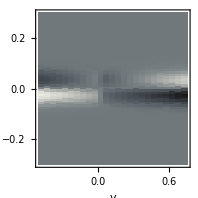

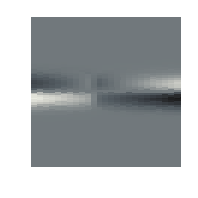

```mathematica
cm=72/2.54;
size=7.0cm; (*7.4, 6.7*)
fe=Show[diffTblCatch2d, ImageSize->size]

axes=Graphics3D[{},AbsoluteOptions[fe]];
(*fig=Show[fe,BoxStyle->Directive[Opacity[0]],Boxed->False,AxesStyle->Directive[Opacity[0]]]*)
fig=Show[fe,FrameStyle->Directive[Opacity[0]],Frame->False,AxesStyle->Directive[Opacity[0]]]

Export["~thomasbuhrmann/Downloads/Axes.pdf",axes,Background->None];
Export["~thomasbuhrmann/Downloads/Fig.pdf",Rasterize[fig,ImageResolution->600, Background->None,ColorSpace->"RGB"](*/.{255,255,255,255}->{0,0,0,0}*),Background->None];
(*a=Import["~thomasbuhrmann/Downloads/Axes.pdf"];
b=Import["~thomasbuhrmann/Downloads/Fig.eps"];
fef = Show[b,a]

Export["~thomasbuhrmann/Downloads/FinalFig.pdf",fef]*)
(*
Rastered3d[sensedInputCatch3d,figExpPath<>"SMECatch3d",size,Options[G3D]];

Rastered3d[sensedInputAvoid3d,figExpPath<>"SMEAvoid3d",size,Options[G3D]];
Rastered3d[epTblBi3dCatch,figExpPath<>"EPsCatch3d",size,Options[G3D]];
Rastered3d[epTblBi3dAvoid,figExpPath<>"EPsAvoid3d",size,Options[G3D]];
*)
```

```mathematica
>
```

### Change in sensor as result of moving towards EP

-0.246925

0.656675

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

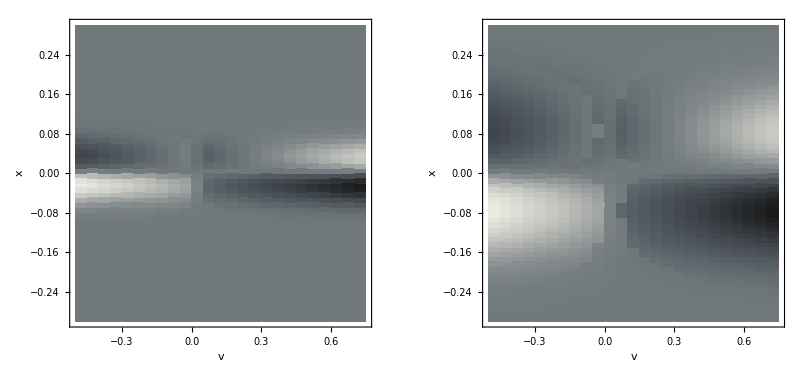

```mathematica
(* Can't really calculate, as EP velocity, and therefore changes in sensed values, is bistable? *)
dims=Dimensions[epTblBiCatchRpl];
nC=dims[[1]];
mC=dims[[2]];
dims=Dimensions[epTblBiAvoidRpl];
nA=dims[[1]];
mA=dims[[2]];
(*
velCh= (2*epTblBiCatch-1)*dt;
velCh2=Table[(2*epTblBiCatch[[i,j]]-1)*dt,{i,1,nC,1},{j,1,mC,1}];
*)

xFori[i_,w_]:=-0.3+i*0.01;
vForj[j_]:=-0.5+j*0.05;

min=Min[2*epTblBiCatchRpl-1]
max=Max[2*epTblBiCatchRpl-1]

(*  Small change in velocity as small proportion of difference between eventual (steady-state) and current velocity. *)
velCh3Catch=Table[((2*epTblBiCatchRpl[[i,j]]-1)-(vForj[j-1]))*0.5,{i,1,nC,1},{j,1,mC,1}];
velCh3Avoid=Table[((2*epTblBiAvoidRpl[[i,j]]-1)-(vForj[j-1]))*0.5,{i,1,nA,1},{j,1,mA,1}];
GraphicsRow[{
ListPlot3D[velCh3Catch,DataRange->{{-0.5,0.75},{-0.3,0.3}},ViewPoint->cam],
ListPlot3D[velCh3Avoid,DataRange->{{-0.5,0.75},{-0.3,0.3}},ViewPoint->cam]},ImageSize->800]

(* tbl1: Actual sensed values of differential sensor *)
(* tbl2: Differential sensor values after moving a small proportion towards attractor *)
tbl1Catch=Table[(Sensed[xFori[i,ww]+vForj[j]*dt,hh,ww]-Sensed[xFori[i,ww],hh,ww])/dt,{i,0,nC-1,1},{j,0,mC-1,1}];
tbl2Catch=Table[(Sensed[xFori[i,ww]+vForj[j]*dt+velCh3Catch[[i+1,j+1]]*dt,hh,ww]-Sensed[xFori[i,ww]+vForj[j]*dt,hh,ww])/dt,{i,0,nC-1,1},{j,0,mC-1,1}];

(* Same for avoidance case *)
tbl1Avoid=Table[(Sensed[xFori[i,www]+vForj[j]*dt,hh,www]-Sensed[xFori[i,www],hh,www])/dt,{i,0,nA-1,1},{j,0,mA-1,1}];
tbl2Avoid=Table[(Sensed[xFori[i,www]+((vForj[j]+velCh3Avoid[[i+1,j+1]])*dt),hh,www]-Sensed[xFori[i,www]+vForj[j]*dt,hh,www])/dt,{i,0,nA-1,1},{j,0,mA-1,1}];

GraphicsRow[{ListPlot3D[tbl1Catch,PlotRange->All,AxesLabel->{"v","x"},DataRange->{{-0.5,0.75},{-0.3,0.3}},ViewPoint->cam],
ListPlot3D[tbl1Avoid,PlotRange->All,AxesLabel->{"v","x"},DataRange->{{-0.5,0.75},{-0.3,0.3}},ViewPoint->cam] },ImageSize->800]

GraphicsRow[{ListPlot3D[tbl2Catch,PlotRange->All,AxesLabel->{"v","x"},DataRange->{{-0.5,0.75},{-0.3,0.3}},ViewPoint->cam],
ListPlot3D[tbl2Avoid,PlotRange->All,AxesLabel->{"v","x"},DataRange->{{-0.5,0.75},{-0.3,0.3}},ViewPoint->cam] },ImageSize->800]

(* Difference in sensor value after moving a small proportion towards attractor *)
diffTblCatch=ListPlot3D[tbl2Catch-tbl1Catch,PlotRange->All,AxesLabel->{"v","x"},ColorFunction->(ColorData["GrayTones"][#3]&),Mesh->None,DataRange->{{-0.5,0.75},{-0.3,0.3}},ViewPoint->cam];
diffTblAvoid=ListPlot3D[tbl2Avoid-tbl1Avoid,PlotRange->{Automatic,Automatic,{-5,5}},AxesLabel->{"v","x"},ColorFunction->(ColorData["DarkRainbow"][#3]&),Mesh->None,DataRange->{{-0.5,0.75},{-0.3,0.3}},ViewPoint->cam];

GraphicsRow[{diffTblCatch,diffTblAvoid},ImageSize->800]

(* As density plots *)
diffTblCatch2d=ListDensityPlot[tbl2Catch-tbl1Catch,PlotRange->All,AxesLabel->{"v","x"},ColorFunction->ColorData[colScheme],ColorFunctionScaling->True,InterpolationOrder->0,Mesh->None,DataRange->{{-0.5,0.75},{-0.3,0.3}}];
diffTblAvoid2d=ListDensityPlot[tbl2Avoid-tbl1Avoid,PlotRange->{Automatic,Automatic,{-5,5}},ColorFunction->ColorData[colScheme],ColorFunctionScaling->True,InterpolationOrder->0,AxesLabel->{"v","x"},Mesh->None,DataRange->{{-0.5,0.75},{-0.3,0.3}}];

GraphicsRow[{diffTblCatch2d,diffTblAvoid2d},ImageSize->800]
(*
Rastered[diffTblCatch2d,figExpPath<>"SMHCatch",225,Options[G2D2]]
Rastered[diffTblAvoid2d,figExpPath<>"SMHAvoid",225,Options[G2D2]]
*)
```

## CTRNN analysis: single node

### Redefine CTRNN

```mathematica
neuron= DynamicalSystem[
{(-y+w σ[y+θ]+J)/τ},
{{y,-maxp,maxp}},
{{w,-maxp,maxp},
{θ,-maxp,maxp},
{J,-20,20},
{τ,0.5,20}}];

couple =DynamicalSystem[
{(-y1+w11 σ[y1+θ1]+w21 σ[y2+θ2]+J)/τ1,(-y2+w12 σ[y1+θ1]+w22 σ[y2+θ2])/τ2},
{{y1,-maxp,maxp},{y2,-maxp,maxp}},
{{w11,-maxp,maxp},{w12,-maxp,maxp},{w21,-maxp,maxp},{w22,-maxp,maxp},{θ1,-maxp,maxp},{θ2,-maxp,maxp},{τ1,0.5,20},{τ2,0.5,20},{J,-20,20}}];

hidden = neuron/.{w->7.54563,θ->-4.0057,τ->1.0,J->0};
output = neuron/.{w->0.0,θ->1.57389,τ->1.0,J->0};
inW=9.79266;

network = couple/.{w11->7.54563,w21->0,w12->-2.07816, w22->0.0,θ1->-4.0057,θ2->1.57389,τ1->1.0,τ2->1.0,J->0};
With[{ε=10^-5},networko=TransformDynamicalSystem[network,{{o1,ε,1-ε},{o2,ε,1-ε}},{σ[y1+θ1],σ[y2+θ2]}]];
With[{ε=10^-5},hiddeno=TransformDynamicalSystem[hidden,{{o,ε,1-ε}},{σ[y+θ]}]];
With[{ε=10^-5},outputo=TransformDynamicalSystem[output,{{o,ε,1-ε}},{σ[y+θ]}]];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

### Hidden neuron phase portraits

```mathematica
input=-10;
Manipulate[DisplayPhasePortrait[hiddeno/.J->input],{input,-10,10}]
```

```mathematica
EquilibriumPoints[hidden/.J->21.0]
```

{EquilibriumPoint[Stable,Node,{28.5456}]}

### Output neuron phase portrait

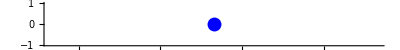

0.828337

```mathematica
DisplayPhasePortrait[outputo/.J->0]
EquilibriumPoints[outputo/.J->0][[1,3,1]]
Manipulate[DisplayPhasePortrait[outputo/.J->input],{input,-10,10}]
```

### Hidden neuron bifurcation diagram

DisplayBifurcationDiagram::optx: Unknown option {GridLinesStyle} in {GridLinesStyle → Dashing[{Small, Small}], GridLines → {{0}, {0}}}.

{BifurcationPoint[Fold,{5.68448280810384},{J → -0.674546224845672, w → 7.54563, θ → -4.0057, τ → 1.}],BifurcationPoint[Fold,{2.32691719189616},{J → 1.14031622484567, w → 7.54563, θ → -4.0057, τ → 1.}]}

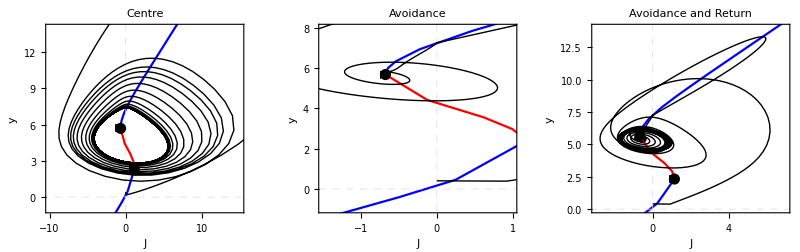

```mathematica
bifPl=DisplayBifurcationDiagram[hidden,J,GridLinesStyle->Dashed,GridLines->{{0},{0}}];
$BifurcationDiagramBPs

(* Overlay actual trajectories *)
duration=5;
startAt=0;
SetStartEnd[1];
phPlN1F=PhasePlot["NeuralOutput0","NeuralState1",i0,in,{},inW];
phPlN2F=PhasePlot["NeuralOutput0","NeuralState2",i0,in,{},inW];
bifPhPl1=Show[bifPl,phPlN1F,PlotRange->{{-10,15},{-1,14}},PlotLabel->"Centre",AspectRatio->1.0];

SetStartEnd[2];
phPlN1A=PhasePlot["NeuralOutput0","NeuralState1",i0,in,{},inW];
phPlN2A=PhasePlot["NeuralOutput0","NeuralState2",i0,in,{},inW];
bifPhPl2=Show[bifPl,phPlN1A,PlotRange->{{-1.5,1},{-1,8}},PlotLabel->"Avoidance",AspectRatio->1.0];

(* Show detail of avoidance behaviour, and long-term return to gaussian *)
duration=10.0;SetStartEnd[2];
phPlN1AFull=PhasePlot["NeuralOutput0","NeuralState1",i0,in,{},inW];
bifPhPl2Full=Show[bifPl,phPlN1AFull,PlotRange->{{-3,7},{0,14}},PlotLabel->"Avoidance and Return",AspectRatio->1.0];

GraphicsRow[{bifPhPl1,bifPhPl2,bifPhPl2Full},ImageSize->800]
```

## CTRNN analysis: two-node

### 2d Bifurcation diagram

```mathematica
range1={{-10,10},{0,10},{-2,0}};
range2={{-3,3},{3,9},{-2.5,-1}};
netBifPl=DisplayBifurcationDiagram[network,J,PlotRange->{-10,10}];
$BifurcationDiagramBPs;
bif1J=$BifurcationDiagramBPs[[1,1,9,1,2]]
bif2J=$BifurcationDiagramBPs[[2,1,9,1,2]]

duration=5.0;
SetStartEnd[1];
trjN12FPl=PhasePlot3d["NeuralOutput0","NeuralState1","NeuralState2",i0,in,{},inW];

SetStartEnd[2];
trjN12APl=PhasePlot3d["NeuralOutput0","NeuralState1","NeuralState2",i0,in,{},inW];

GraphicsRow[{Show[netBifPl,trjN12FPl,PlotRange->range1],Show[netBifPl,trjN12APl,PlotRange->range2]},ImageSize->800]
(*Rasterize[%,ImageResolution->200]*)
```

-0.674546224845672

1.14031622484567

-Graphics-

### Projections

DisplayBifurcationDiagram::optx: Unknown option {ImageSize} in {StateVariables → {y1}, PlotRange → {{-2, 2}, {-3, 10}}, ImageSize → 300}.

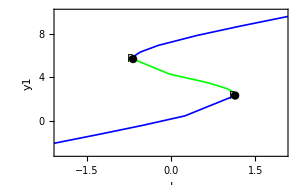

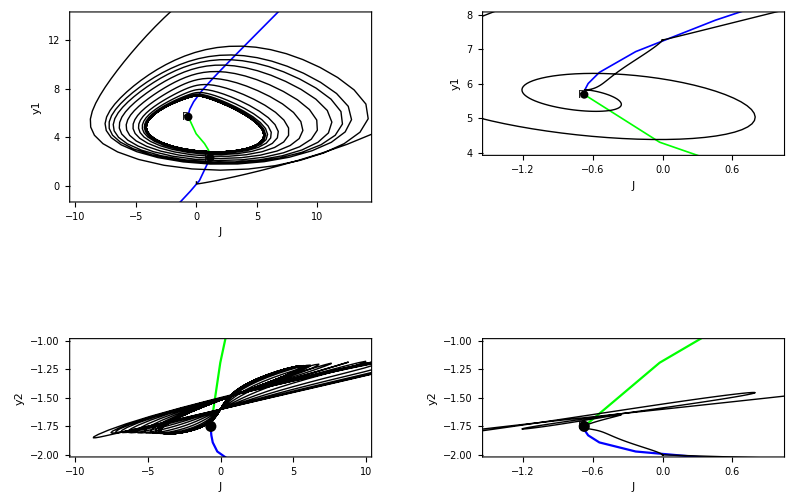

```mathematica
bi1=DisplayBifurcationDiagram[network,J,StateVariables->{y1},PlotRange->{{-2,2},{-3,10}},ImageSize->300]
bi2=DisplayBifurcationDiagram[network,J,StateVariables->{y2}];
phPlY1F=Show[bi1,phPlN1F,PlotRange->{{-10,14},{-1,14}}];
phPlY1A=Show[bi1,phPlN1A,PlotRange->{{-1.5,1},{4,8}}];
phPlY2F=Show[bi2,phPlN2F,PlotRange->{{-10,10},{-2,-1}}];
phPlY2A=Show[bi2,phPlN2A,PlotRange->{{-1.5,1},{-2,-1}}];
GraphicsGrid[{{phPlY1F,phPlY1A},{phPlY2F,phPlY2A}},ImageSize->800]
(*Rasterize[%,ImageResolution->200]*)

(*
Export[figExpPath<>"BifurcationCatch.eps",phPlY1F,ImageSize->225]
Export[figExpPath<>"BifurcationAvoid.eps",phPlY1A,ImageSize->225]
*)
(*
tmp=Show[phPlY1F,AspectRatio->1/GoldenRatio,Options[G2D2]]
Export[figExpPath<>"BifurcationCatch.eps",tmp,ImageSize->225]
tmp=Show[phPlY1A,AspectRatio->1/GoldenRatio,Options[G2D2]]
Export[figExpPath<>"BifurcationAvoid.eps",tmp,ImageSize->225]
tmp=Show[bi1,AspectRatio->1/GoldenRatio,Options[G2D2]]
Export[figExpPath<>"Bifurcation.eps",tmp,ImageSize->225]
*)
```

### 2d Phase portraits around bifurcation points (in neural output space)

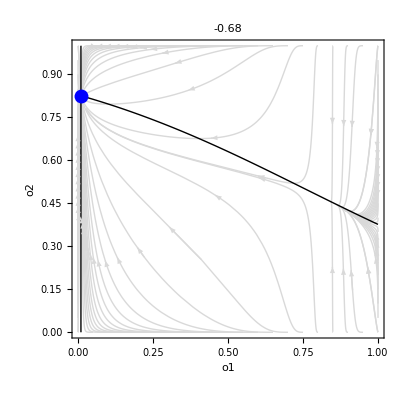
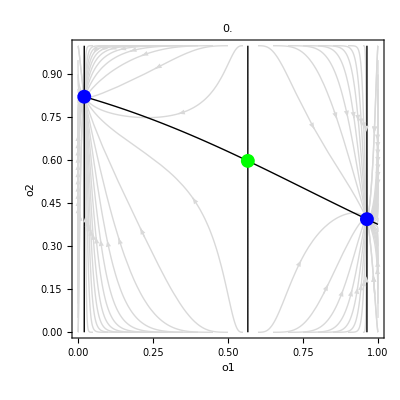
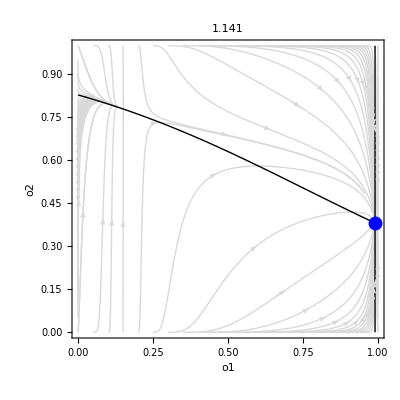

```mathematica
FlowPortrait[input_,dur_:6.0,numPoints_:20]:=Show[DisplayFlow[networko/.J->input,dur,PlotPoints->numPoints,FlowPlotMode->Boundary,PlotStyle->{LightGray}],DisplayPhasePortrait[networko/.J->input,NullManifolds->True,NullManifold2Style->{Black}],PlotLabel->input];

(*inputs={-0.7,-0.6,1.0,1.15};*)
inputs={-0.68,0.0,1.141};
flowPortraits=Table[FlowPortrait[x,10.0,20],{x,inputs}];
(*flowPortraits=Partition[flowPortraits,2];*)
(*GraphicsGrid[flowPortraits,ImageSize->800]*)
row=Row[flowPortraits]
```

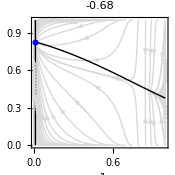

```mathematica
size=175;
tmp=Show[row[[1,1]],PlotRangePadding->0, Options[G2D2],ImageSize->size]
Export[figExpPath<>"PhasePortrait1.eps",tmp];
tmp=Show[row[[1,2]],PlotRangePadding->0, Options[G2D2],ImageSize->size];
Export[figExpPath<>"PhasePortrait2.eps",tmp];
tmp=Show[row[[1,3]],PlotRangePadding->0, Options[G2D2],ImageSize->size];
Export[figExpPath<>"PhasePortrait3.eps",tmp];
```

```mathematica
epIn=0;
eps=EquilibriumPoints[networko/.J->epIn]
eps[[1,3,2]]
Manipulate[FlowPortrait[input,5,20],{input,-10,10}]
```

{EquilibriumPoint[Stable,Node,{0.0208731, 0.822081}],EquilibriumPoint[Saddle,Node,{0.566122, 0.598062}],EquilibriumPoint[Stable,Node,{0.963078, 0.394714}]}

0.822081